```mathematica
sample={983,984,987,987,987,990,990,985,989,989,989,990,990,991,992,995,997,1001,1001,1003,1003,1005,1006,1007,1011,1012,1012,1012,1025,1026,1032,1029};
```

```mathematica
max=2^31-1
```

2147483647

```mathematica
min=-2^31
```

-2147483648

```mathematica
2^64-1-min^2 *4
```

-1

```mathematica
Floor[max^2 *4/31]
```

595056259888054272

```mathematica
min^2 *4
```

18446744073709551616

```mathematica
Floor[(2^64/31)]
```

595056260442243600

```mathematica
Floor[2^63/31*2]
```

595056260442243600

```mathematica
2^62/8
```

576460752303423488

```mathematica
2^62
```

4611686018427387904

```mathematica
2^7
```

128

```mathematica
overflowsample={min,min,min,min,min,min,min,min,min,min,min,min,min,min,min,min,max,max,max,max,max,max,max,max,max,max,max,max,max,max,max,max};
```

```mathematica
Total[overflowsample]
```

-16

```mathematica
Mean[overflowsample]
```

-1/2

```mathematica
Floor[StandardDeviation[overflowsample]]
```

2181845567

```mathematica
2^64-(-2^31)^2*4
```

0

```mathematica
Floor[Sum[overflowsample[[i]]^2,{i,1,32}]/31]
```

4760450081321191490

```mathematica
Floor[Sqrt[4760450081321191488]+1/2]
```

2181845568

```mathematica
4760450081321191488
```

```mathematica
√191.
```

13.8203

```mathematica
√(2^30)
```

32768

```mathematica
N[√(2^31-2^29)]
```

40132.4

```mathematica
guess[i_]:=Ceiling[√(2^64/2^i*(√2)/2)];
```

```mathematica
Table[guess[i],{i,0,64}]
```

{3611622603,2553802834,1805811302,1276901417,902905651,638450709,451452826,319225355,225726413,159612678,112863207,79806339,56431604,39903170,28215802,19951585,14107901,9975793,7053951,4987897,3526976,2493949,1763488,1246975,881744,623488,440872,311744,220436,155872,110218,77936,55109,38968,27555,19484,13778,9742,6889,4871,3445,2436,1723,1218,862,609,431,305,216,153,108,77,54,39,27,20,14,10,7,5,4,3,2,2,1}

```mathematica
2^32
```

4294967296

```mathematica
Floor[√(2^64-1)]
```

4294967295

```mathematica
(2^32-1)^1
```

4294967295

```mathematica
54.29+6.67
```

60.96

```mathematica
approxroot[x_]:=(6+9x)/(13+2x)
```

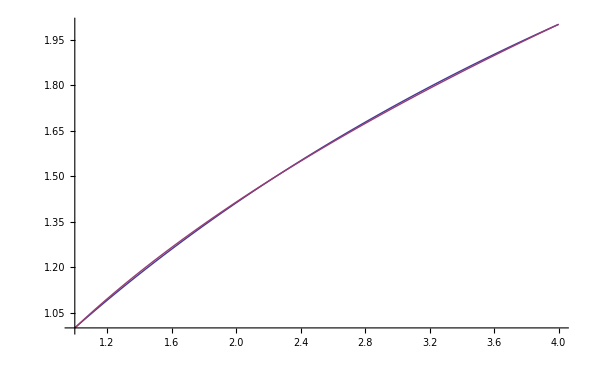

```mathematica
Plot[{approxroot[x],√x},{x,1,4}]
```